# PROJEKTY

## Úvodní slovo

autosave defaultně nastavený není 
(Mathematica -> Preferences -> Advanced -> Open Option Inspector -> Notebook Options -> File Options -> NoteookAutoSave -> True)

Znaky a matematické výrazy
	a) Používejte palety
	b) Zkratky: Esc + symbol + Esc

SlideShow

Formátování

Clear, QuitKernel, Abort evaluation (Ctrl + .)

Projekty:
	a) skupiny po (1), 2 nebo 3
	b) příprava: pondělí cca 1 hod, úterý 1 hod
	c) prezentace: v úterý (max 10 min)
	d) výstup pro slpnění zápočtu je jakýsi protokol
		= komentovaný notebook s výsledky (1 za skupinu)

Projekt 1

Studujte následující dynamický systém:

x[n+1] = f (x[n])                                                        
f (x) = a · x · (1 - x) , kde a ∈ ⟨0,4⟩

Příklad pro x[0] = 0.53 a a = 3.46:
  x ⟶ 0.53 → 0.86 → 0.41 → 0.86 → 0.41 → 0.86 → 0.41 → ....

Úkoly:
   1) Zvolte x[0] a a.
   2) Vypište 100 následujících bodů.
   3) Vykreslete posloupnost bodů graficky.
   4) Jak daný vývoj ovlivní parametr a a jak parametr x.
   5) Vysvětlete pojmy: konvergence, periodicita, kvazi-periodicita, chaos

Pokročilé úkoly: 
   6) Nakreslete bifurkační diagram.
   7) Co je to atraktor?
   8) Nakreslete tzv. pavoučí diagram:

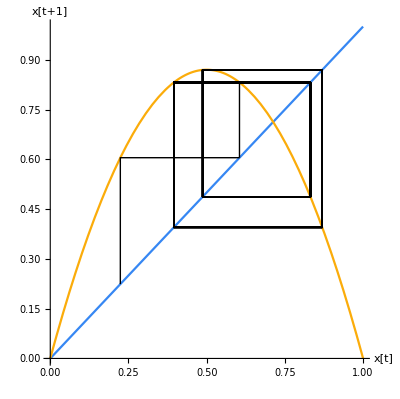

Užitečné funkce: Table, NestList, ListPlot, Manipulate,  Plot, Graphics, Show, Function, Line, (DynamicModule, For)

Projekt 2

Uvažujme SIR (Susceptible, Infectious, or Recovered) model šíření infekčních nemocí.

-Graphics-

Model je popsaný systémem diferenciálních rovnic:

S’ = - β S I       
I’ = β S I - ν I
R’ = ν I

kde platí, že N = S + I + R je celá populace. A počet vyléčených R lze tedy dopočítat R = N - S - I a stačí řešit první dvě diferenciální rovnice.

Mějme uzavřenou populaci N = 5000, ostrov na který přijíždí loď. V čase t = 0 se vrátí na ostrov jeden z obyvatel a je nakažený, tj. S(0)  = 1 (určete ostatní počáteční podmínky). Nakreslete graf, jak se chovají počty náchylných, nakažlivých a vyléčených (imunních) v průběhu 200 dnů.  
Použijte následující hodnoty parametrů ν = 0.1 (pacient je infekční 10 dní),  R_0 = 2.5, kde R_0 =  β/νN je tzv. reprodukční číslo, počet lidí, které nakazí jeden nemocný.
Zjistěte rozdíl v chování pro R_0 = 2.5 a R_0 = 1.7. Kdy nákaza vrcholí, kolik je maximální počet nakažených a kolik je na konci nákazy imunních.

Užitečné funkce: DSolve, NDSolve, DSolveValue, Plot, ListPlot, ParametricPlot, Graphics, Show, Manipulate, Function

Projekt 3

Vyčíslování chemických reakcí zvládnout žáci SŠ i ZŠ. Dokážete ale naprogramovat funkci, která za vás vyčíslí libovolnou reakci?

Úkoly:
  1) Vyčísli nádledující chemickou reakci:
				KNO3 + C ⟶ Κ2CΟ3 + CΟ + Ν2
	a) Vyčísli reakci na papíře.	
	b) Použij funkci Solve.
	c) Použij maticový zápis a vyřeš danou lineární maticovou rovnici.

2) Vyčísli pomocí swMathematica následující ‘crazy’ chemickou reakci:
		[Cr(urea)6]3[Cr(CN)6]2 + K2Cr2O7 + H2SO4 ⟶ Κ2SΟ4 + ΚΝΟ3 + Cr2(SΟ4)3 + CΟ2 + Η2Ο
[urea = CH4N2O]

Pokročilé úkoly: 
  3) Napište funkci, která vyčíslí libovolnou reakci.
Příklad pro reakci z úlohy 1:

In:  	vycisli[input_, output_] := ....
	vycisli[{{k,n,3*o}, c} , {{2*k},{c,o},{2*n}}]
Out:	? kno3 + ? c ⟶ ? k2co3 + ? co + ? n2

Užitečné funkce: Solve, Print, MatrixPower, Transpose, EigenSystem, Subscript, Function, (For, If)

Projekt 4

Integrujte numericky pomocí metody Monte Carlo.

-Graphics-

Úkoly:
  1) Do čtverce o hraně 2 zakreslete jednotkovou kružnici
  2) Vygenerujte N (pseudo)náhodných bodů rovnoměrně (uniform distribution) rozmístěných ve čtverci.
  3) Vypočítejte obsah kruhu a numericky určete π.
  	(výsledek ověřte analyticky = v ruce nebo pomocí funkce Integrate)
  4) Vekreslete závislost přesnosti vašeho π na N.
  	(zakreslete statistickou chybu)

Pokročilé úkoly:
  5) Vyberte si vlastní 3D útvar nebo nějaký složitější 2D útvar (např.: https://www.desmos.com/calculator/dnzfajfpym), který zintegrujte pomocí metody Monte Carlo.

Užitečné funkce: Plot, RandomReal, Integrate, Function, ListPlot, Point, Piecewise, Total, For, If, Switch

Projekt 5

Pohrajte si s vykreslováním molekul.

-Graphics-

Úkoly:
  1) Vykreslete molekulu/molekulový systém.
  2) Vypište souřeadnice všech atomů.
  3) Přidejte do grafu vzdálenost 2 vybraných atomů.
  4) Vykreslete vodíkové interakce.
  5) Zanimujte finální obrázek tak, aby vám v prezentaci rotoval (+ exportujte gif).

Užitečné funkce: Import, Export, Sort, DistanceMatrix, MatrixForm, Graphics3D, Show, Line, Text, Style, Manipulate, ViewPoint, SphericalRegion, If, For, Dashed, ChemicalData

Projekt 6

Naučte se zpracovávat komplexnější data ze souboru (ex4.csv):

-Graphics-

Úkoly:
  1) Kolik je v souboru mužů a kolik žen?
  2) Jaká je nejmenší hmotnost?
  3) Jak se jmenuje nejtěžší člověk?
  4) Kdo je nejstarší?
  5) Jaká je průmerná hmotnost všech vs mužů vs žen? (+ přidejte statistickou chybu)
  6) Kdo má nejdelší jméno?
  7) Nakreslete korelaci mezi kapitálem a váhou.
  8) Nakreslete histogram bydlišť všech zaměstnanců.
  
Pokročilé úkoly:
  9) Vygenerujte pro každého zaměstnance vlastní soubor (např.: .txt), ve které bude uloženo:

prijmeni.txt
	Jméno a Přijmení: xxx
	Bydliště: xxx
	Datum Narození: xxx

Užitečné funkce: Import, Sort, ListPlot, AbsoluteTime, TimeDifference, If, Cases, Patterns, StringSplit, StringLength, Mean, Max, Min, StandardDeviation, Switch, ToString, Evaluate, Print, For, Total, Histogram, BarChart, For

Projekt X

Vymyslete si vlastní projekt.

Např.:
	- Pendulum
	- Fraktály
	- Naprogramuj hru
	- Zanalyzuj vlastní dat
	- Práce s vlnovými funkcemi (spektrometrie)
	- Machine Learning
	- Model dravec a kořist
	.....

Projekt 1 - dynamický systém
Projekt 2 - SIR model šíření nákazy (soust. dif. rovnic)
Projekt 3 - vyčíslování  reakcí (soust. rovnic)
Projekt 4 - integrace MC
Projekt 5 - vizualizace molekul
Projekt 6 - práce se souborem
Projekt X